## Images

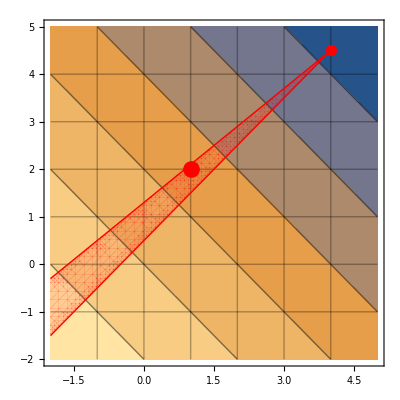

```mathematica
Show[ContourPlot[-x-y,{x,-2,5},{y,-2,5},Mesh->6,MeshFunctions->{#1&,#2&}],ParametricPlot[{t,4/5 t+13/10},{t,-2,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,t+1/2},{t,-2,4},PlotStyle->{Red,Thick}],RegionPlot[{-x+y>= 1/2&&4 x-5 y>= -13/2},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],Graphics[{PointSize[.02],Red,Point[{4,4.5}]}],Graphics[{PointSize[.03],Red,Point[{1,2}]}]]
```

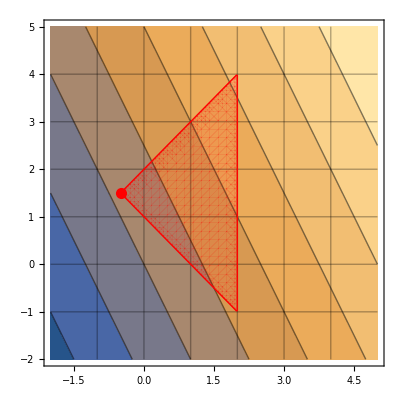

```mathematica
Show[ContourPlot[2 x+y,{x,-2,5},{y,-2,5},Mesh->6,MeshFunctions->{#1&,#2&}],RegionPlot[{x+y>= 1&&x-y>= -2&&-x>= -2},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->{Red,Thick},PlotPoints->40],Graphics[{PointSize[.02],Red,Point[{-1/2,3/2}]}]]
```

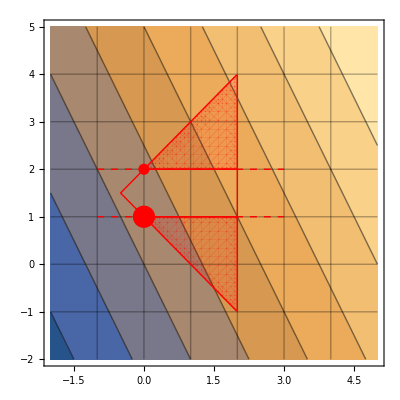

```mathematica
Show[ContourPlot[2 x+y,{x,-2,5},{y,-2,5},Mesh->6,MeshFunctions->{#1&,#2&}],RegionPlot[{x+y>= 1&&x-y>= -2&&-x>= -2&&y>= 2},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->{Red,Thick},PlotPoints->40],RegionPlot[{x+y>= 1&&x-y>= -2&&-x>= -2&&y≤1},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->{Red,Thick},PlotPoints->40],Graphics[{PointSize[.02],Red,Point[{0,2}]}],Graphics[{PointSize[.04],Red,Point[{0,1}]}],ParametricPlot[{x,1},{x,-1,3},PlotStyle->{Thick,Red,Dashed}],ParametricPlot[{x,2},{x,-1,3},PlotStyle->{Thick,Red,Dashed}],RegionPlot[{x+y≥1&&x-y≥-2&&-x≥-2&&y≤2&&y≥1},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[0]},BoundaryStyle->{Red,Thin},PlotPoints->40]]
```

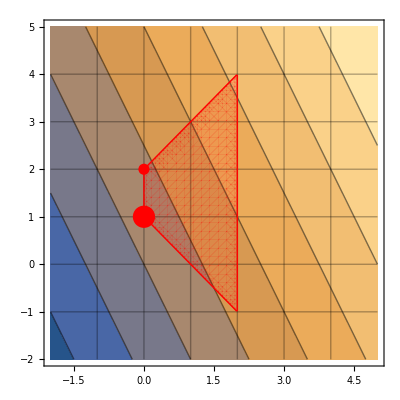

```mathematica
cut1=Show[ContourPlot[2 x+y,{x,-2,5},{y,-2,5},Mesh->6,MeshFunctions->{#1&,#2&}],RegionPlot[{x+y>= 1&&x-y>=-2&&-x>= -2&&x>= 0},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->{Red,Thick},PlotPoints->40],Graphics[{PointSize[.04],Red,Point[{0,1}]}],Graphics[{PointSize[.02],Red,Point[{0,2}]}]]
```

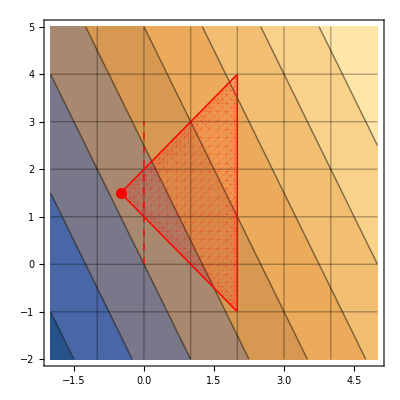

```mathematica
cut2=Show[ContourPlot[2 x+y,{x,-2,5},{y,-2,5},Mesh->6,MeshFunctions->{#1&,#2&}],ParametricPlot[{0,t},{t,0,3},PlotStyle->{Red,Dashed,Thick}],RegionPlot[{x+y>= 1&&x-y>=-2&&-x>= -2},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->{Red,Thick},PlotPoints->40],Graphics[{PointSize[.02],Red,Point[{-1/2,3/2}]}]]
```

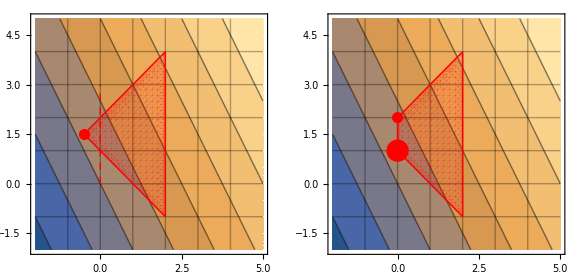

```mathematica
GraphicsGrid[{{cut2,cut1}},ImageSize->Large]
```

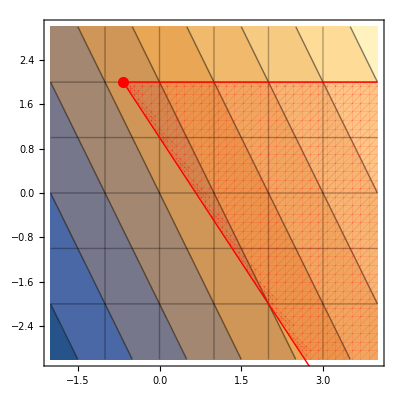

```mathematica
Show[ContourPlot[2 x+y,{x,-2,4},{y,-3,3},Mesh->5,MeshFunctions->{#1&,#2&}],RegionPlot[{3/2 x+y>=1&&-y>= -2},{x,-2,4},{y,-3,3},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],ParametricPlot[{t,1-3/2t},{t,-.65,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,2},{t,-.65,4},PlotStyle->{Red,Thick}],Graphics[{PointSize[.02],Red,Point[{-2/3,2}]}]]
```

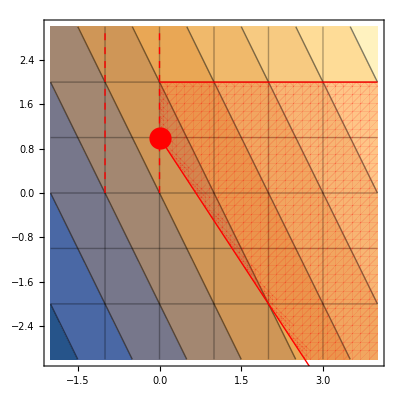

```mathematica
Show[ContourPlot[2 x+y,{x,-2,4},{y,-3,3},Mesh->5,MeshFunctions->{#1&,#2&}],RegionPlot[{3/2 x+y>= 1&&-y>= -2&&x>= 0},{x,-2,4},{y,-3,3},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],ParametricPlot[{t,1-3/2t},{t,0,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,2},{t,0,4},PlotStyle->{Red,Thick}],Graphics[{PointSize[.04],Red,Point[{0,1}]}],ParametricPlot[{-1,y},{y,0,3},PlotStyle->{Thick,Red,Dashed}],ParametricPlot[{0,y},{y,0,3},PlotStyle->{Thick,Red,Dashed}]]
```

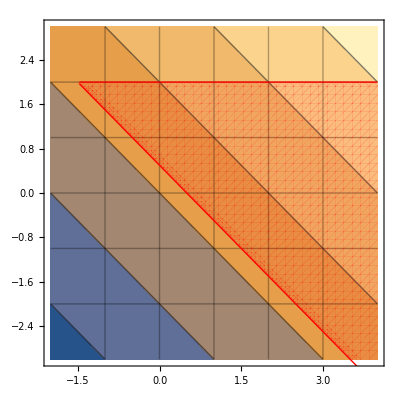

```mathematica
except1=Show[ContourPlot[x+y,{x,-2,4},{y,-3,3},Mesh->5,MeshFunctions->{#1&,#2&}],RegionPlot[{ x+y>= .5&&-y>= -2},{x,-2,4},{y,-3,3},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],ParametricPlot[{t,.5-t},{t,-1.47,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,2},{t,-1.47,4},PlotStyle->{Red,Thick}]]
```

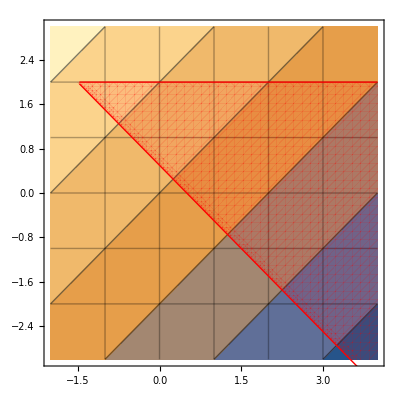

```mathematica
except2=Show[ContourPlot[-x+y,{x,-2,4},{y,-3,3},Mesh->5,MeshFunctions->{#1&,#2&}],RegionPlot[{ x+y>= .5&&-y>= -2},{x,-2,4},{y,-3,3},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],ParametricPlot[{t,.5-t},{t,-1.47,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,2},{t,-1.47,4},PlotStyle->{Red,Thick}]]
```

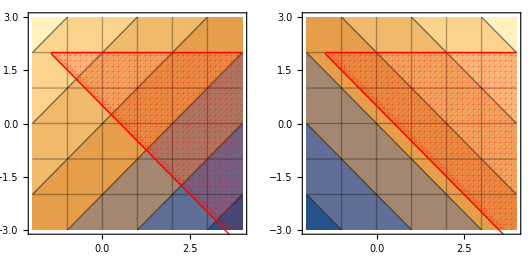

```mathematica
GraphicsGrid[{{except2,except1}}]
```

## Modeling Problem 15

Variables:  xi = # violins made in quarter i using regular labor,
	      yi = # violins made in quarter i using overtime,
	      hi = # violins in inventory at end of quarter i.

```mathematica
vars={x1,x2,x3,x4,y1,y2,y3,y4,h1,h2,h3,h4};
```

Objective function: The sum of production (200 per violin made with regular labor, 300 per violin made with overtime) and inventory costs (25 per violin held in inventory).

```mathematica
objective=200 (x1+x2+x3+x4)+300(y1+y2+y3+y4)+25(h1+h2+h3+h4);
```

Constraints:

```mathematica
constraints=
h1==6-5+x1+y1&&
h2==h1-4+x2+y2&&
h3==h2-3+x3+y3&&
h4==h3-3+x4+y4&&
x1≤2&&
x2≤2&&
x3≤2&&
x4≤2&&
x1≥0&&x2≥0&&x3≥0&&x4≥0&&
y1≥0&&y2≥0&&y3≥0&&y4≥0&&
h1≥0&&h2≥0&&h3≥0&&h4≥0;
```

Mathematica's solution

```mathematica
Minimize[{objective,constraints},vars]
```

{2000,{x1→2,x2→2,x3→2,x4→2,y1→0,y2→0,y3→0,y4→1,h1→3,h2→1,h3→0,h4→0}}

Interpretation of solution

Mathematica's solution says that the minimum cost is $2,000 which can be acheived by making 2 violins during each quarter using regular labor, and using overtime labor in the fourth quarter to make one violin.

## Modeling Problem 7

Variables:  xi = number of full-time employees starting on day i, hi = number of half-time employees starting on day i.  Day 1=Sunday, day 2=Monday, etc.

```mathematica
vars={x1,x2,x3,x4,x5,x6,x7,h1,h2,h3,h4,h5,h6,h7};
```

Objective function: The total cost for the employer is the sum of each employee's wages (hourly rate times number of hours per day times number of days worked).

```mathematica
objective=10*8*5(x1+x2+x3+x4+x5+x6+x7)+8*4*5(h1+h2+h3+h4+h5+h6+h7);
```

Constraints:

```mathematica
constraints=
8(x1+x4+x5+x6+x7)+4(h1+h4+h5+h6+h7)≥400&&
8(x1+x2+x5+x6+x7)+4(h1+h2+h5+h6+h7)≥200&&
8(x1+x2+x3+x6+x7)+4(h1+h2+h3+h6+h7)≥200&&
8(x1+x2+x3+x4+x7)+4(h1+h2+h3+h4+h7)≥250&&
8(x1+x2+x3+x4+x5)+4(h1+h2+h3+h4+h5)≥250&&
8(x2+x3+x4+x5+x6)+4(h2+h3+h4+h5+h6)≥300&&
8(x3+x4+x5+x6+x7)+4(h3+h4+h5+h6+h7)≥400&&
 (h1+h2+h3+h4+h5+h6+h7)≤.25 (x1+x2+x3+x4+x5+x6+x7+h1+h2+h3+h4+h5+h6+h7)&&
x1≥0&&x2≥0&&x3≥0&&x4≥0&&x5≥0&&x6≥0&&x7≥0&&h1≥0&&h2≥0&&h3≥0&&h4≥0&&h5≥0&&h6≥0&&h7≥0;
```

Mathematica's solution

```mathematica
Minimize[{objective,constraints},vars]
```

{20238.1,{x1→0.,x2→0.,x3→0.,x4→11.3095,x5→12.5,x6→8.33333,x7→12.5,h1→4.16667,h2→0.,h3→4.16667,h4→6.54762,h5→0.,h6→0.,h7→0.}}

Interpretation of solution

Mathematica's solution says that the lowest total cost for the employer to meet its labor requirements is met by parts of workers! 

If we instead force the variables to be integers, we get the following solution.  Notice that this solution is not simply a rounded-off version of the above.

```mathematica
Minimize[{objective,constraints},vars,Integers]
```

{20400.,{x1→0,x2→0,x3→2,x4→20,x5→2,x6→19,x7→2,h1→4,h2→0,h3→0,h4→11,h5→0,h6→0,h7→0}}

## Simple Example

```mathematica
Minimize[{-x-y,-x+y≥0.5&&4 x-5 y≥-13/2},{x,y}]
```

{-8.5,{x→4.,y→4.5}}

```mathematica
Minimize[{-x-y,-x+y≥0.5&&4 x-5 y≥-13/2},{x,y},Integers]
```

{-3.,{x→1,y→2}}

```mathematica
Show[ContourPlot[-x-y,{x,-2,5},{y,-2,5},Mesh->6,MeshFunctions->{#1&,#2&}],ParametricPlot[{t,4/5 t+13/10},{t,-2,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,t+1/2},{t,-2,4},PlotStyle->{Red,Thick}],RegionPlot[{-x+y>= 1/2&&4 x-5 y>= -13/2},{x,-2,5},{y,-2,5},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],Graphics[{PointSize[.02],Red,Point[{4,4.5}]}],Graphics[{PointSize[.03],Red,Point[{1,2}]}]]
```

-Graphics-

## Branching Fails

```mathematica
except1=Show[ContourPlot[-x+y,{x,-2,4},{y,-3,3},Mesh->5,MeshFunctions->{#1&,#2&}],RegionPlot[{ x+y>= .5&&-y>= -2},{x,-2,4},{y,-3,3},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],ParametricPlot[{t,.5-t},{t,-1.47,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,2},{t,-1.47,4},PlotStyle->{Red,Thick}]]
```

-Graphics-

```mathematica
except2=Show[ContourPlot[x+y,{x,-2,4},{y,-3,3},Mesh->5,MeshFunctions->{#1&,#2&}],RegionPlot[{ x+y>= .5&&-y>= -2},{x,-2,4},{y,-3,3},AxesLabel->{"x","y"},PlotStyle->{Opacity[.1],Red},BoundaryStyle->None,PlotPoints->40],ParametricPlot[{t,.5-t},{t,-1.47,4},PlotStyle->{Red,Thick}],ParametricPlot[{t,2},{t,-1.47,4},PlotStyle->{Red,Thick}]]
```

-Graphics-

## Oil Delivery problem

Variables :  xi = the number of tanks of oil moved through arc i

```mathematica
vars={x1,x2,x3,x4,x5,x6,x7};
```

Objective function: The sum of the unit costs times the number of tanks for each arc.

```mathematica
objective=5*x1+5*x2+2*x3+3*x4+x5+4*x6+2*x7;
```

Constraints:

```mathematica
constraints=
(* in-equals-out *)
10==x1+x2&&
x4==7+x7&&
x5+x6+x7==3&&
x1==x3+x4&&
x3==x5&&
x2==x6&&
(* no negative numbers of tanks *)
x1≥0&&
x2≥0&&
x3≥0&&
x4≥0&&
x5≥0&&
x6≥0&&
x7≥0;
```

Mathematica's solution

```mathematica
Minimize[{objective,constraints},vars]
```

{80,{x1→10,x2→0,x3→3,x4→7,x5→3,x6→0,x7→0}}

Interpretation of solution

Mathematica's solution says that one cost-minimizing delivery scheme is to send all ten tanks from the source through arc 1, then 7 tanks through arc 4 (to the city with demand 7) and 3 tanks first through arc 3, then through arc 5 (to the city with demand 3).